### Definition

```mathematica
a=Rationalize@0.1;
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=Rationalize@0.4;u0=10^-20;δstart=10^-10;m=1;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=N[- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r]];V[r_]=-α/r;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
RealEigenEnergy[n_]=-(m α^2)/(2 n^2);
Table20REE=Table[RealEigenEnergy[n],{n,20}]
```

{-2/25,-1/50,-2/225,-1/200,-2/625,-1/450,-2/1225,-1/800,-2/2025,-1/1250,-2/3025,-1/1800,-2/4225,-1/2450,-2/5625,-1/3200,-2/7225,-1/4050,-2/9025,-1/5000}

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
{e,SetPrecision[0.9999#[[10]],6],SetPrecision[1.0001#[[10]],6]}&[Table20REE]
```

{e,-0.00079992,-0.00080008}

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{ef,evShifted},
PrintTemporary[V];
Module[{shift=10,d=2000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
Table[
PrintTemporary[n];
Module[{sol,evnew,steps=∞,time1,time2},
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,opt1];
evnew=e/.
FindRoot[u[e][min]==0/.sol,If[n<5,{e,SetPrecision[0.99#[[n]],6],SetPrecision[1.01#[[n]],6]}&[evShifted],{e,SetPrecision[0.99#[[n]],6],SetPrecision[1.01#[[n]],6]}&[Table20REE]],opt2(*,StepMonitor:>PrintTemporary[e]*)]],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])(*u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]*)/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
(*PrintTemporary["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
PrintTemporary[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
PrintTemporary[{estart,eend}];
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}]]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]];
δexpminus9=δ50e[10^-9,V[r]];
δexpminus5=δ50e[10^-5,V[r]];
(*δ50V=δ50[V[r]]*)
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000799356024108875307158800370015696288485754568172) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00252779037141606535634764484961214551074983799219) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.258100960992136653725175035849101347847353159394) is less than WorkingPrecision (50.).

### Determine c_1

```mathematica
hhhc1[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,c1]-δexpminus10,8];
Determinec1[{start_,end___},opt___]:=Module[{aaa,findroot,mon},aaa=a;
Print[aaa];
Monitor[findroot=FindRoot[hhhc1[10^-10,c1]==δexpminus10,{c1,start,end},opt,StepMonitor:>{mon={c1,evnhhhc1[c1]}}],mon];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1[{-0,-1},{MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50}]
```

1

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000908232447133165221769633976714347114447920773153) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000870330704250347656591120392624588844514461336242) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-3.8076753361368637473447970520437066117508894569944

-3.8076753361368637473447970520437066117508894569944

#### Vs_1’s eigensystem

```mathematica
AbsoluteTiming@EigenEnergy[V[r],αSch,{10^-15,Which[n<7,1000,7≤n<11,2000,11≤n<15,3000,15≤n<19,5000,n≥19,8000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->200}];
{First@%,(Last@%-Table20REE)/Table20REE}
```

{-0.08,-0.02,-0.00888889,-0.005,-0.0032,-0.00222222,-0.00163265,-0.00125,-0.000987654,-0.0008,-0.000661157,-0.000555556,-0.000473373,-0.000408163,-0.000355556,-0.0003125,-0.000276817,-0.000246914,-0.000221607,-0.0002}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{2772.03,{5.919468698133×10^-17,-3.57091692342884×10^-15,5.46917590296×10^-17,-9.5312911239913×10^-16,-3.76231642038037×10^-15,-7.1727953213716×10^-16,-1.22590155688994×10^-15,-1.508599484489×10^-16,-2.1764213064365×10^-16,-6.1302187525873×10^-16,-1.13614296484874×10^-15,-1.3029793693899×10^-16,-8.078377192829×10^-17,-8.999888174856×10^-17,4.5280420568839×10^-16,6.3393402280769×10^-16,7.9516255472625×10^-16,9.0592615291054×10^-16,1.05060509693582×10^-15,9.6602048729907×10^-16}}

```mathematica
AbsoluteTiming[energyVs1=EigenEnergy[Vs1[r,a,c1],αSch,{10^-15,Which[n<7,1000,7≤n<11,2000,11≤n<15,3000,15≤n<19,4000,n≥19,8000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->If[n==1,1000,200]}]];
N[%,6]
```

{-0.0816888,-0.0200457,-0.00889477,-0.00500139,-0.00320045,-0.0022224,-0.00163274,-0.00125004,-0.000987678,-0.000800014,-0.000661166,-0.000555561,-0.000473377,-0.000408166,-0.000355557,-0.000312501,-0.000276817,-0.00024689,-0.000221014,-0.000195602}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{2230.35,{-0.0816889,-0.0200457,-0.00889477,-0.00500139,-0.00320045,-0.0022224,-0.00163274,-0.00125004,-0.000987678,-0.000800014,-0.000661166,-0.000555561,-0.000473377,-0.000408166,-0.000355557,-0.000312501,-0.000276818,-0.000246914,-0.000221607,-0.0002}}

```mathematica
N@Table20REE
```

{-0.08,-0.02,-0.00888889,-0.005,-0.0032,-0.00222222,-0.00163265,-0.00125,-0.000987654,-0.0008,-0.000661157,-0.000555556,-0.000473373,-0.000408163,-0.000355556,-0.0003125,-0.000276817,-0.000246914,-0.000221607,-0.0002}

```mathematica
(energyVs1-Table20REE)/Table20REE
```

{0.02111065553464902245808538939,0.00228355250904738163809628435,0.00066161208120322274751408233,0.00027704282005731129845146513,0.00014136882205487415767497269,0.00008166328051282104812269087,0.000051371115059972116388347,0.00003439077306141253265148221,0.00002414231920745395352724881,0.00001759382375712946268970255,0.00001321521786635156108959128,0.00001017716576042581326049387,8.00344614530603835949687×10^-6,6.40726512158540820231044×10^-6,5.20885818640295723538145×10^-6,4.2916399348915695515233×10^-6,3.57774251429159170078135×10^-6,3.01380685233233846185662×10^-6,2.56243443235727174667035×10^-6,2.19688367097203284194347×10^-6}

```mathematica
efVs1=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{Which[n<11,2000,11≤n<15,3000,15≤n<19,4000,n≥19,6000],If[n<12,1.*10^-40,1.*10^-30]},WorkingPrecision->50,PrecisionGoal->20,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->10^-5];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
];
```

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0816888524427719217966468311511 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00500138521410028655649225732565 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00163273693243275097488389934204 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00080001407505900570357015176204 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000661165762127514943180885680188 f[r],f[3000]==1.×10^-40,f'[3000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00320045238023057559730455991262 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00125004298846632676566581435276 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0200456710501809476327619256869 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00055556120953653356989625582993 f[r],f[3000]==1.×10^-30,f'[3000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00222240369617891738010693931305 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000987678165253538226126940492655 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00889476988516625086886679184293 f[r],f[2000]==1.×10^-40,f'[2000]==-1.×10^-40},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000473376569678648665580288519228 f[r],f[3000]==1.×10^-30,f'[3000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000355557407594021832162572580071 f[r],f[4000]==1.×10^-30,f'[4000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000276817599375090461340263192068 f[r],f[4000]==1.×10^-30,f'[4000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000221607216051951768924486796754 f[r],f[6000]==1.×10^-30,f'[6000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000408165880516376157309470330791 f[r],f[3000]==1.×10^-30,f'[3000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000312501341137479653615484851032 f[r],f[4000]==1.×10^-30,f'[4000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000246914324396753662305793051017 f[r],f[4000]==1.×10^-30,f'[4000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000200000439376734194406568388694 f[r],f[6000]==1.×10^-30,f'[6000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\psir_a=1_efVs1.mx",efVs1];
```

#### ψ_r Vs_1

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000221607216051951768924486796754 f[r],f[4000]==1.×10^-30,f'[4000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

{1.92297×10^15                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}

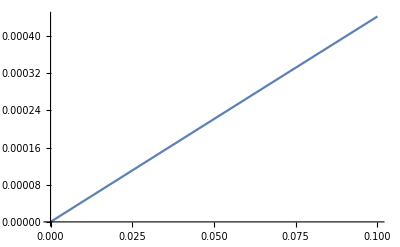

```mathematica
Module[{n=19},Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>10,4000,2000],1.*10^-30},WorkingPrecision->50,PrecisionGoal->20,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->10^-5]]
Plot[%,{r,0,0.1},AxesOrigin->{0,0}]
```

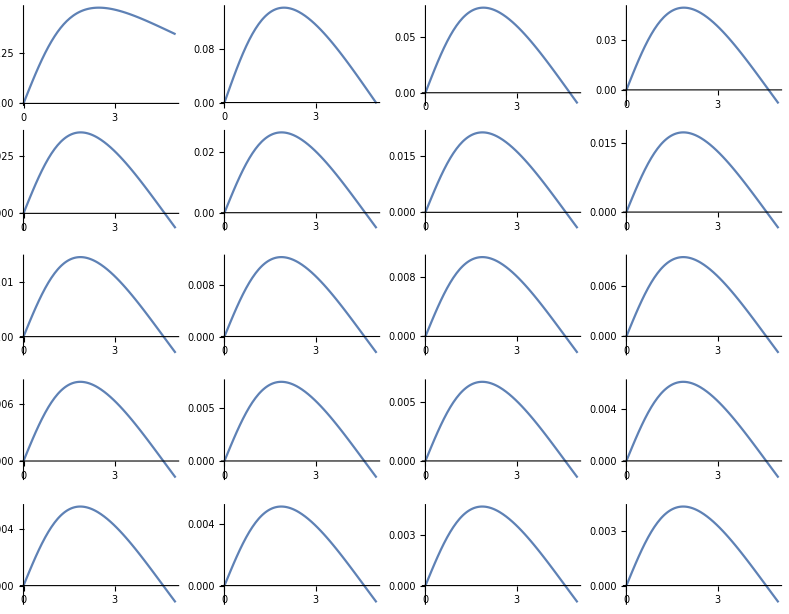

```mathematica
GraphicsGrid@Partition[Plot[efVs1[[#]],{r,0,5},ImageSize->Small,AxesOrigin->{0,0}]&/@Range@20,4]
```

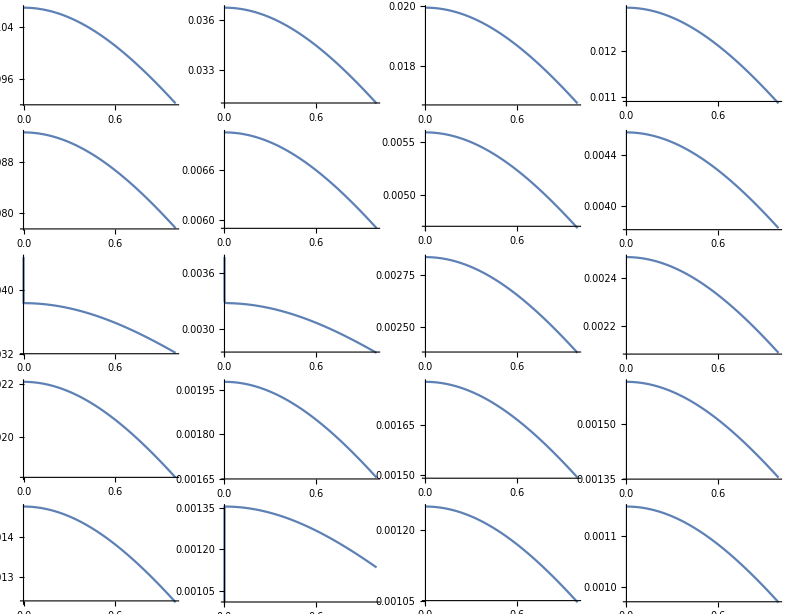

```mathematica
GraphicsGrid@Partition[Plot[efVs1[[#]]/(√(4π)r),{r,0,1},ImageSize->Small]&/@Range@20,4]
```

```mathematica
IntegrationVs11st=NIntegrate[efVs1[[#]]/(√(4π)r)δa[r] r^2,{r,0,4000},WorkingPrecision->30]&/@Range@20;
```

NIntegrate::precw: The precision of the argument function (2.050625953853×10^-311 ⅇ^(-r^2/2) r «1»[r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (-5.16297×10^-132 ⅇ^(-«1») r InterpolatingFunction[{{9.9999999999999992929287939988014500233064511906197×10^-41,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«13317»},{NDSolve`LocalSeries,NDSolve`LocalSeries,«47»,NDSolve`LocalSeries,«13317»}}}][r]) is less than WorkingPrecision (30.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {4.9409693916851470622583181305317819318271984098446332494752165497697972578752672}. NIntegrate obtained 0.0019579629408899985274373114380879446036551485749358193933801877953051294294341839 and 3.8062309634513299100535163339146441264675946204224709645945834593851632838932412×10^-21 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (3.42585×10^-72 ⅇ^(-«1») r InterpolatingFunction[{{9.9999999999999992929287939988014500233064511906197×10^-41,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«11186»},{NDSolve`LocalSeries,NDSolve`LocalSeries,«47»,NDSolve`LocalSeries,«11186»}}}][r]) is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.2777667938737321720291525363795566052289769191999724581575718021997851557311078}. NIntegrate obtained 0.0010507748878961756933933780834990257820559636006518594306984680999639898183394881 and 1.9701082367828065050101904194772542164745703294553532124179997406726016908666206×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {3.2777667938737321720291525363795566052289769191999724581575718021997851557311078}. NIntegrate obtained 0.00067929990865138755586671456911408477084513800375476855593173628767292320344115701 and 1.2541481567692431499635936724846017628072818251805297094060102849911726357830985×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
ψrTrueVs1[n_][γ_]:=4π(γ IntegrationVs11st[[n]])
```

```mathematica
DetermineVs1[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=Limit[RS[#,r]/(√(4π)),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs1[#][γ]&/@REFRANGE==REF],{γ,0,1},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{r0,γ}(*,N[ERROR,6]*)/.RES
]
```

```mathematica
DetermineVs1[0]
```

{0,2.10161969142106854058720178462}

```mathematica
Module[{γη},
γlVs1={};
Monitor[Table[
γη=DetermineVs1[r0];
AppendTo[γlVs1,γη];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

FindRoot::precw: The precision of the argument function ({0.000759304420357189881134669625285 γ==0.00159577}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({0.000759304420357189881134669625285 γ==0.00159513}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({0.000759304420357189881134669625285 γ==0.00159449}) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

```mathematica
γrVs1=Interpolation[γlVs1]
```

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
ψrfunVs1[r_][n_]:=4π(γrVs1[r] IntegrationVs11st[[n]])
```

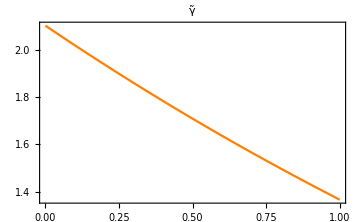

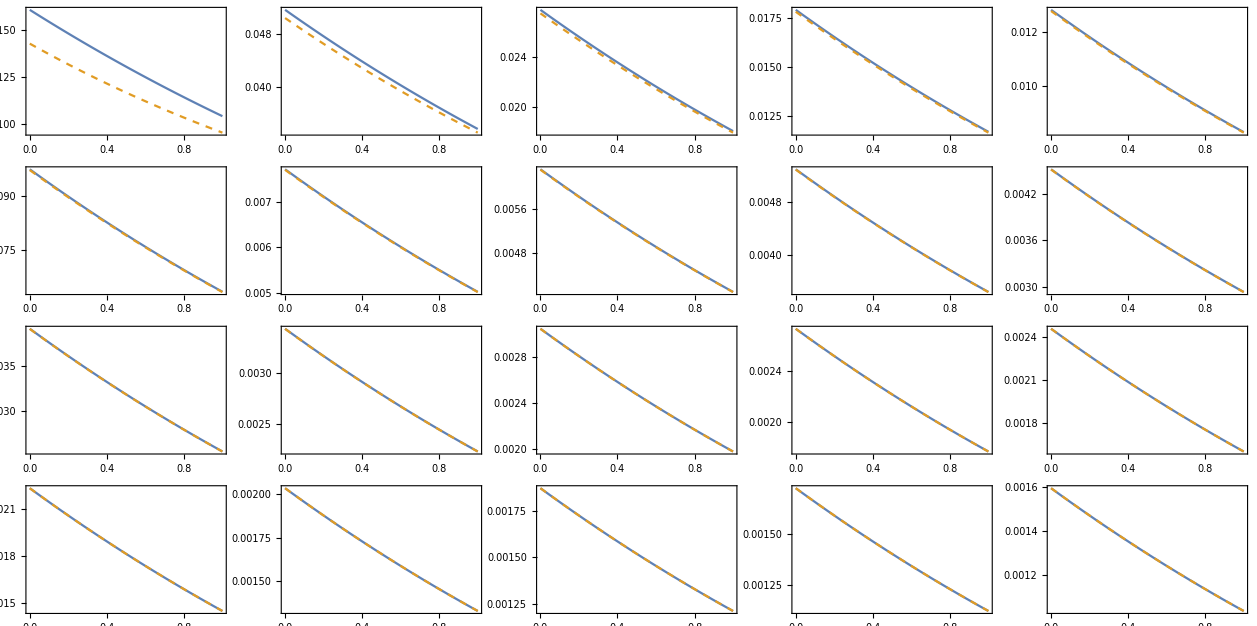

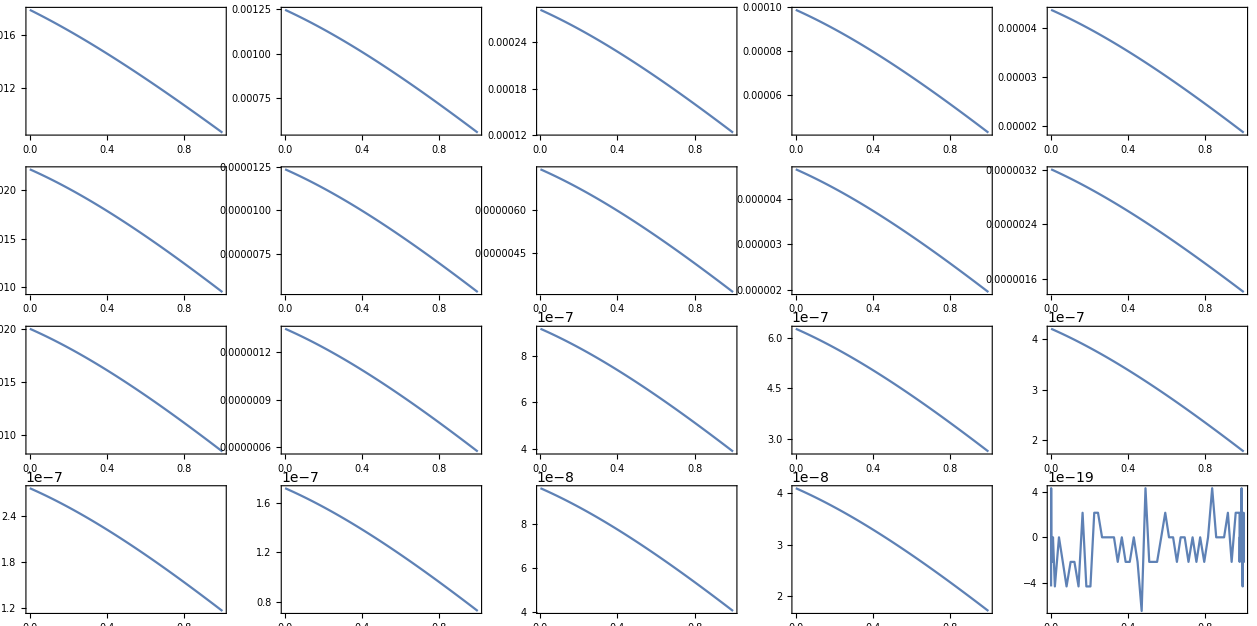

```mathematica
GraphicsGrid@{{Plot[γrVs1[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃",Frame->True]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs1[r][n],RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
GraphicsGrid@Partition[Table[Plot[{ψrfunVs1[r][n]-RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
```

```mathematica
∇^2 Subscript[ψ, r] Subscript[Vs, 1]
```

```mathematica
lap[f_,r_]:=Simplify[(2 D[f,r])/r+D[f,{r,2}]]
```

```mathematica
lappsi=lap[efVs1[[#]]/(√(4π)r),r]&/@Range@20
```

{1/r 3.229655891777×10^-310                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1/r 8.13147×10^-131                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1/r 5.39559×10^-71                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1/r 1.59126×10^-40                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1/r 7.47621×10^-22                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1/r 3.87746×10^-9                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1/r 7.13237                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1/r 8.40609×10^7                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1/r 3.18347×10^13                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1/r 1.02242×10^18                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1/r 9.55979×10^7                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-1/r 440.524                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1/r 3.70845×10^6                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-1/r 8.6201×10^9                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1/r 2119.52                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],-1/r 5.49243×10^6                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],1/r 5.53126×10^9                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],-1/r 2.47037×10^12                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r],1/r 1.58012                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 6000.0000000000000000000000000000000000000000000000}}, <>][r],-1/r 2761.25                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 6000.0000000000000000000000000000000000000000000000}}, <>][r]}

```mathematica
ψrTruelap[n_][γ_]:=4π(γ IntegrationVs11st[[n]])
```

```mathematica
DeterminelapVs1[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[RS[#,r]/(√(4π)),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ]&/@REFRANGE==REF],{γ,0,1},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ}}/.RES
]
```

```mathematica
DeterminelapVs1[0.1]
```

FindRoot::precw: The precision of the argument function ({0.000759304420357189881134669625285 γ==-0.0122617}) is less than WorkingPrecision (30.).

{{0.1,-16.148550044714810674777205407}}

```mathematica
Quiet@Module[{max=1,interval=0.001},
(*Zl=Determine[0][[1]];*)γllapVs1={};(*ηl={};*)
Monitor[Table[Module[{γη},
γη=DeterminelapVs1[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllapVs1,γη[[1]]];
(*AppendTo[ηl,γη[[2]]];*)]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

End

```mathematica
γrlapVs1=Interpolation[γllapVs1]
```

InterpolatingFunction[{{0.01, 1.}}, <>]

```mathematica
ψrfunlapVs1[r_][n_]:=4π(γrlapVs1[r] IntegrationVs11st[[n]])
```

```mathematica
lapRS[r_]=lap[RS[n,r]/(√(4π)),r]
```

1/(375 n^(7/2) r)8 ⅇ^(-(2 r)/(5 n)) √(2/(5 π)) (3 (-5 n+r) Hypergeometric1F1[1-n,2,(4 r)/(5 n)]-(-1+n) (3 (5 n-2 r) Hypergeometric1F1[2-n,3,(4 r)/(5 n)]-2 (-2+n) r Hypergeometric1F1[3-n,4,(4 r)/(5 n)]))

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

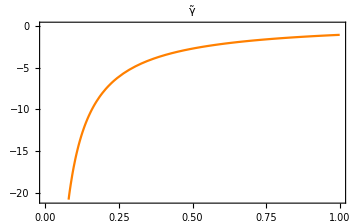

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

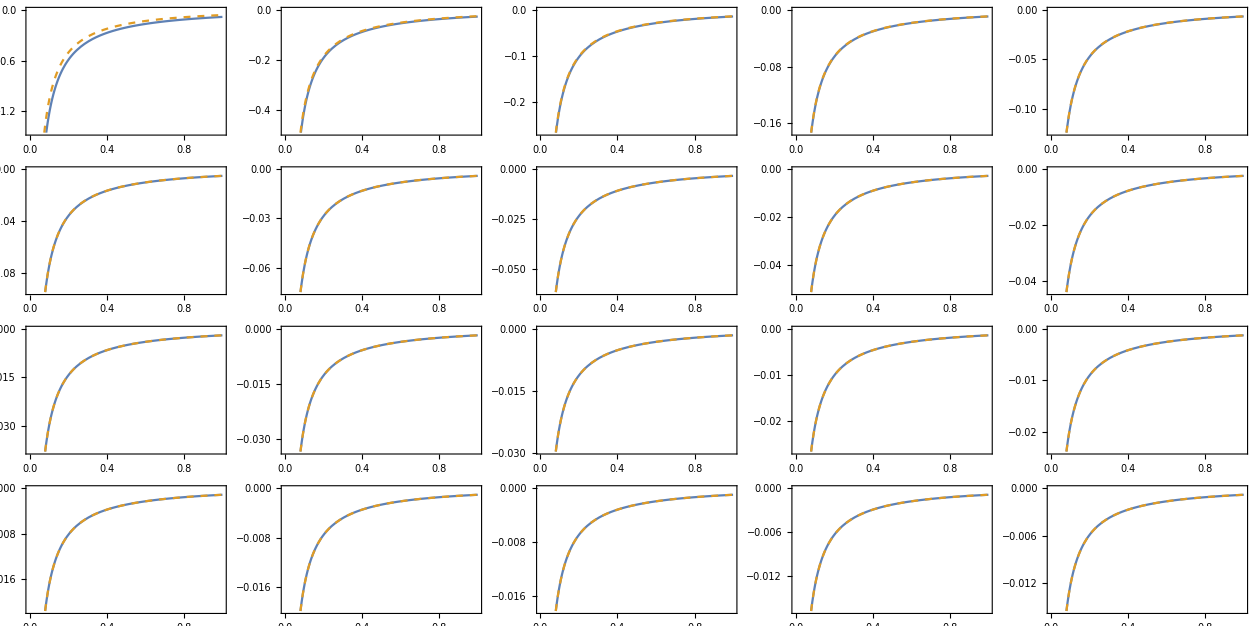

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

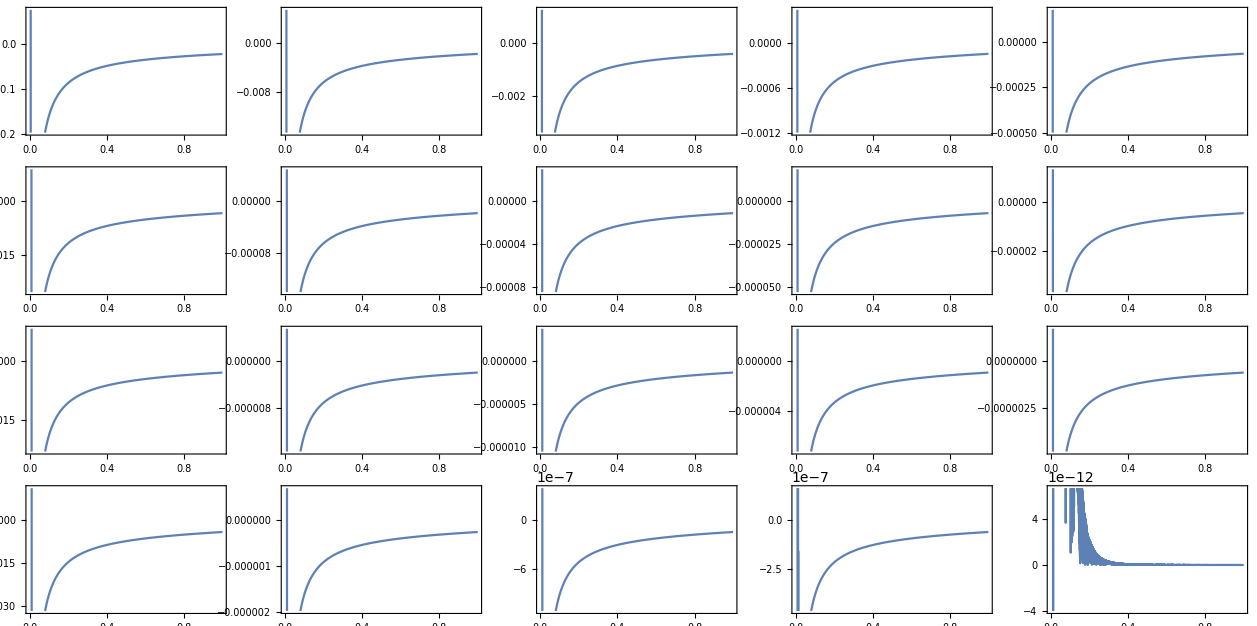

```mathematica
GraphicsGrid@{{Plot[γrlapVs1[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃",Frame->True]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlapVs1[r][n],lapRS[r]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
GraphicsGrid@Partition[Table[Plot[{ψrfunlapVs1[r][n]-lapRS[r]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
```

### Determine c_2 & d_1

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus5,8];
```

```mathematica
Determinec2d1[{c2start_,c2end___},{d1start_,d1end___}]:=Module[{findroot,mon},
Monitor[findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus5},{{c2,c2start,c2end},{d1,d1start,d1end}},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>{mon={c2,d1,evnhhh1,evnhhh2}}],mon];
{c2,d1}/.findroot
]
```

```mathematica
Remove[c2,d1,hhh,evnhhh1,evnhhh2]
```

```mathematica
{c2,d1}=Determinec2d1[{-6},{0.5}]
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+0.380962 Power[«2»]-0.5 Plus[«2»]+1. Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00071619821791746368773586873382713613327837949716) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/100000+0.380962 Power[«2»]-0.5 Plus[«2»]+1. Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.23039435424540094800222171113130004245254631422) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+0.380962 Power[«2»]-0.5 Plus[«2»]+1. Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00071619821791746368773586873382713613327837949716) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\Coulomb_psir_comparasion_c2d1.mx",{c2,d1}];
```

```mathematica
ContourPlot[{hhh[ee[[1]],c2,d1]-δexpminus10,hhh[ee[[2]],c2,d1]-δexpminus5},{c2,10,-10},{d1,-10,10},PlotPoints->100]
```

#### Vs_2’s eigensystem

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{10^-15,Which[n<10,1000,11≤n<15,1800,15≤n<19,6000,n≥19,8000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.001249,-0.001251},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[20]]=%
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.001385,-0.0013851},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[19]]=%
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.001543,-0.0015433},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[18]]=%
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.001730,-0.001731},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[17]]=%
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.001953,-0.0019532},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[16]]=%
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.0022221,-0.0022223},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[15]]=%
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\Coulomb_psir_comparasion_energyVs2.mx",energyVs2];
```

```mathematica
(energyVs2-Table20REE)/Table20REE
```

```mathematica
efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]
```

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=Limit[RS[n,r]/(√(4π)),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=Determine[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[1]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γr[r] Integration1st[[n]]+ηr[r] a^2 Integration2nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```